Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 8: Funciones de varias variables I (Funciones, límites). Notas y prácticas

## Funciones de varias variables.

## Definir una función de varias variables. Evaluar una función de varias variables Dibujar la gráfica de una función de dos variables (en rectángulos o en otros recintos) Dibujar curvas de nivel de una función de dos variables (ContourPlot) Estudio del límite de una función de dos variables (límites reiterados, direccionales, por conjuntos)

Una función real de varias variables reales es una aplicación de un subconjunto de D de ℝ^n en ℝ, 
f: D⊂ℝ^n ⟶ℝ. D es el dominio de la función. En ocasiones, solo nos dan la expresión de f, y debemos entender que el dominio es donde tenga sentido la expresión matemática.

Para definir en el Mathematica una función de varias variables el proceso es similar. Basta poner todas las variables de la que dependa la función.

```mathematica
f[x_,y_,z_]:= x Cos[y] + z Sin[x]
```

Una vez definida la función se puede evaluar en uno o varios puntos.

```mathematica
f[1,0,0]
```

1

```mathematica
{f[2,1,0],f[2,-1,0],f[0,0,0]}
```

{2 Cos[1],2 Cos[1],0}

La gráfica de una función de una variable real está en ℝ^2. La gráfica de una función de dos variables está en ℝ^3. En general, la gráfica de una función de n variables estaría en ℝ^(n+1). 
	Graf(f)={(x_1, x_2, ..., x_n, f(x_1, x_2, ..., x_n))∈ℝ^(n+1)/(x_1, x_2, ..., x_n))∈Dom(f)}
Para dibujar gráficas, nos debemos limitar a funciones de dos variables.

```mathematica
g[x_,y_]:= x^2+ y^2
```

```mathematica
Plot3D[g[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Si queremos dibujar la gráfica en otro conjunto que no sea un rectángulo de lados paralelos a los ejes, podemos utilizar la función Which y restringir el recinto donde dibujamos.

```mathematica
Plot3D[Which[x^2+y^2≤9,g[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Para mejorar la gráfica podemos pedir al Mathematica que dibuje más puntos.

```mathematica
Plot3D[Which[x^2+y^2≤9,g[x,y]],{x,-3,3},{y,-3,3}, PlotPoints->100]
```

-Graphics3D-

Otra forma de hacernos una idea de cómo se comporta una función es dibujar sus curvas de nivel.
	Curva de nivel C de la función = {(x,y) ∈ ℝ^2 /  f(x, y) = C}

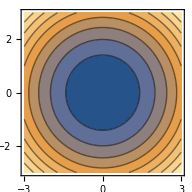

```mathematica
ContourPlot[g[x,y],{x,-3,3},{y,-3,3}]
```

Las curvas de nivel podrían verse como la intersección de la gráfica con planos paralelos a diferentes alturas.

```mathematica
Plot3D[{2,4,6,8,Which[x^2+y^2≤9,g[x,y]]},{x,-3,3},{y,-3,3},PlotPoints->100]
```

-Graphics3D-

En este caso, aparecen dibujadas varias curvas de nivel (el valor se puede ver al pasar el cursor). Todas las curvas de nivel son circunferencias. Líneas más juntas significa que la función varía más rápidamente. Vemos que al alejarnos del (0,0) las curvas de nivel aparecen más juntas, esto significa que la función varía de forma más rápida.

También podemos dibujar sólo una curva de nivel correspondiente a un valor, o varias curvas correspondientes a varios valores.

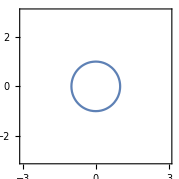

```mathematica
ContourPlot[g[x,y]==1,{x,-3,3},{y,-3,3}]
```

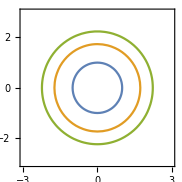

```mathematica
ContourPlot[{g[x,y]==1,g[x,y]==3,g[x,y]==5},{x,-3,3},{y,-3,3}]
```

```mathematica
h[x_,y_]:= Abs[x]+Abs[y]
```

Para dibujar muchas, puede ser más fácil con la función Table.

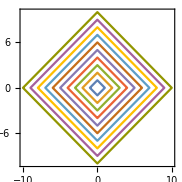

```mathematica
ContourPlot[Evaluate[Table[h[x,y]==i,{i,1,10}]],{x,-10,10},{y,-10,10}]
```

## Dominio de una función

Las funciones de varias variables, como cualquier función, deberían venir dadas con un dominio y una forma de asignar a cada elemento del dominio un número real. Es decir, deberíamos tener una aplicación f: D⊂ℝ^n⟶ ℝ y una forma de calcular f(x_1,...,x_n).  No obstante, en ocasiones nos dan solo la expresión de f y debemos entender que el dominio es todo punto donde tenga sentido desde el punto de vista matemático.

● Encontrar el dominio de las siguientes funciones.

f(x,y) = x^2+y^2, f(x,y) = Log(xy), f(x,y) = 1/(x^2+y^2+1), f(x,y) = √(x^2 + y^2 - 9), f(x,y) = xy/(x^2+y^2), f(x,y) = √(4-2 x^2 - y^2)

● Ejemplo 1.

La función f(x,y) = x^2+y^2, es un polinomio y está definida para cualesquiera valores de las variables x e y. Por tanto, el dominio es ℝ^2.

● Ejemplo 2.

La función f(x,y) = Log(xy) está definida cuando xy>0, es decir los dos valores tienen que ser positivos o los dos negativos y ninguno puede ser cero. Por tanto, el dominio es {(x,y) ϵ ℝ^2/ xy >0}= (-∞, 0)×(-∞, 0) ∪(0,+∞)×(0,+∞)

```mathematica
RegionPlot[x*y>0,{x,-5,5},{y,-5,5}]
```

-Graphics-

● Ejemplo 3.

La función f(x,y) = 1/(x^2+y^2+1), es un cociente de polinomios y estaría definida siempre que el denominador no se anule. En este caso el denominador no puede ser cero y por tanto la función está definida en cualquier punto de ℝ^2.

● Ejemplo 4.

La función f(x,y) = √(x^2 + y^2 - 9), está definida cuando x^2 + y^2 - 9 ≥ 0, serían los puntos de la circunferencia de centro el (0,0) y radio 3, junto con los exteriores. Por tanto, el domino es {(x,y) ϵ ℝ^2/ x^2 + y^2 - 9 ≥ 0}= ℝ^2-{(x,y) ϵ ℝ^2/ x^2 + y^2 < 9 }.

```mathematica
RegionPlot[x^2+y^2>=9,{x,-5,5},{y,-5,5}]
```

-Graphics-

● Ejemplo 5.

La función f(x,y) = xy/(x^2+y^2) es una función racional y por tanto estará definida siempre que no se anule el denominador, en este caso en el punto (0,0). Por tanto, el dominio es {(x,y) ϵ ℝ^2/ (x,y) ≠ (0,0)}= ℝ^2-{(0,0)}

● Ejemplo 6.

La función f(x,y) = √(4-2 x^2 - y^2) está definida cuando el radicando sea positivo o nulo, es decir, 4-2 x^2 - y^2≥ 0. Estos son los puntos del interior y el borde de una elipse centrada en el punto (0,0) y cuyos vértices son los puntos (√2 ,0), (-√2,0), (0, 2), (0, -2) . Por tanto, el dominio es {(x,y) ϵ ℝ^2/ 4≥ 2 x^2 + y^2}.

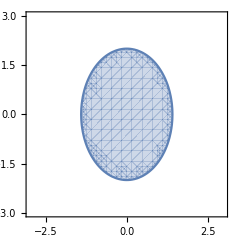

```mathematica
RegionPlot[2x^2+y^2<=4,{x,-3,3},{y,-3,3}]
```

## Cálculo de límites

La mayoría de las funciones con las que trabajamos son continuas (suelen ser múltiplos, sumas, restas, productos, cocientes o composiciones de funciones continuas). Además, conocemos que los polinomios, la exponencial, el logaritmo, el seno, el coseno, ..., son funciones continuas. 

Si la función es continua, el valor del límite en cualquier punto del dominio coincide con el valor de la función (hallar el límite es tan simple como evaluar la función en el punto). También podemos preguntarnos por el límite de una función en un punto que no esté en el dominio, aunque sí “junto” al dominio, o por el límite en el infinito (es decir, cuando nos “alejamos” mucho). 

De manera más formal:
Los límites se pueden estudiar en los puntos de acumulación* del dominio y, si el domino es no acotado, en el infinito.
(*Un punto x_0 ϵ  ℝ^n es un punto de acumulación de un dominio D si toda bola centrada en x_0 contiene puntos de D distintos de x_0 )

Los puntos de acumulación del dominio de una función son los puntos donde podemos hablar propiamente de límite de la función, pues nos podemos acercar a ellos tanto como queramos por puntos del dominio.
De forma similar, para que podamos “acercarnos” al infinito es necesario que el dominio no sea acotado.
(Un conjunto es acotado si puede incluirse en una bola centrada en algún punto de ℝ^n y de radio finito.)

La definición es similar a la que tenemos para funciones de una variable. Una función f tiene límite L en un punto   de acumulación x_0 ϵ  ℝ^n del dominio D, si para cualquier ϵ >0, por pequeño que sea, existe δ>0, que puede ser dependiente de ϵ, tal que todos los puntos x del dominio a distancia de x_0 menor que δ, distinto de x_0, el valor de f en ellos difiere de L en menos de ϵ, es decir, |f(x)-L|<ϵ.

Para la definición de límite de una función, definida en un dominio no acotado, en el infinito, el límite será L, si para cualquier ϵ >0, por pequeño que sea, existe K>0, que puede ser dependiente de ϵ, tal que todos los puntos x del dominio a distancia del origen mayor que K, el valor de f en ellos difiere de L en menos de ϵ, es decir, |f(x)-L|<ϵ.
También podríamos definir límite +∞, cuando la función se hace tan grande como queramos. Análogamente podríamos definir límite -∞.

## Dónde podemos calcular el límite de una función.

Dónde podemos estudiar la existencia de límite de las siguientes funciones.

f(x,y) = x^2+y^2, f(x,y) = Log(xy), f(x,y) = 1/(x^2+y^2+1), f(x,y) = √(x^2 + y^2 - 9), f(x,y) = xy/(x^2+y^2), f(x,y) = √(4-2 x^2 - y^2)

● Ejemplo 1.

El dominio de la función f(x,y) = x^2+y^2 es ℝ^2. Por tanto, podemos estudiar la existencia de límite en cualquier punto de ℝ^2 y en el infinito.

● Ejemplo 2.

El dominio de la función f(x,y) = Log(xy) es {(x,y) ϵ ℝ^2/ xy>0}= (-∞, 0)×(-∞, 0) ∪(0,+∞)×(0,+∞), podemos estudiar la existencia de límite en todos los puntos del domino y además en los puntos de los ejes, donde x ó y se anulan, (por ser puntos de acumulación del dominio) y en el infinito (por ser un conjunto no acotado).

● Ejemplo 3.

El domino de la función f(x,y) = 1/(x^2+y^2+1) es ℝ^2. Por tanto, podemos estudiar la existencia de limite en cualquier punto de ℝ^2 y en el infinito.

● Ejemplo 4.

El dominio de la función f(x,y) = √(x^2 + y^2 - 9) es {(x,y) ϵ ℝ^2/ x^2 + y^2 - 9 ≥ 0}= ℝ^2-{(x,y) ϵ ℝ^2/ x^2 + y^2 < 9 }. Se puede estudiar la existencia del límite en cualquier punto del dominio y en el infinito (no hay puntos de acumulación fuera del domino).

● Ejemplo 5.

El domino de la función f(x,y) = xy/(x^2+y^2) es ℝ^2-{(0,0)}. Por tanto, se puede estudiar la existencia de límite en todos los puntos de ℝ^2 (el punto (0,0) es un punto de acumulación) y en el infinito.

● Ejemplo 6.

El dominio de la función f(x,y) = √(4-2 x^2 - y^2) es {(x,y) ϵ ℝ^2/ 4≥ 2 x^2 + y^2}.  Por tanto, se puede estudiar la existencia de límite en todos los puntos del dominio y en ninguno más, pues no hay puntos de acumulación fuera del domino. Tampoco se puede estudiar el límite en el infinito, pues es un conjunto acotado.

## Cálculo de los límites

Estudiar el valor de los límites, en todos los puntos posibles, de las funciones:

f(x,y) = x^2+y^2, f(x,y) = Log(xy), f(x,y) = 1/(x^2+y^2+1), f(x,y) = √(x^2 + y^2 - 9), f(x,y) = xy/(x^2+y^2), f(x,y) = √(4-2 x^2 - y^2)

● Ejemplo 1.

La función f(x,y) = x^2+y^2 es un polinomio y por tanto continua en todo su dominio, que es ℝ^2. Por tanto,
		lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) = x_0^2+y_0^2
Además, 
		lím_((x,y) ⟶∞)f(x,y) = + ∞
pues dado cualquier valor K por grande que sea, podemos encontrar r tal que f(x,y) en todos los puntos fuera de la bola B((0,0),r)  vale más de K. Podemos tomar r = √K y tenemos que la función f(x,y) valdrá más de K para puntos que estén a una distancia mayor de r del (0,0).

● Ejemplo 2.

La función f(x,y) = Log(xy) es el resultado de aplicar la función logaritmo (que es una función real continua de variable real) al polinomio xy. Por tanto, es una función continua en todo su dominio y tenemos que si (x_0,y_0) está en el dominio
		lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) = Log (x_0 y_0)

Después podríamos estudiar la existencia del límite en los puntos de los ejes, donde x ó y se anulan. 

El límite en cualquier punto de la forma (x_0,0) ó de la forma (0, y_0) de la función xy es cero, de donde Log(x*y) tenderá a menos infinito.
			lím_((x,y) ⟶ (x_0,0_))f(x,y) = -∞,		 lím_((x,y) ⟶ (0,y_0))f(x,y) = -∞

Finalmente podríamos estudiar el límite en el infinito.
		lím_((x,y) ⟶ ∞)f(x,y)
Se trata de ver si hay un valor al que se acerca la función cuando los puntos (x,y) están “muy lejos” del (0.0). Como la función es Log(xy) podemos considerar valores de x e y cuyo producto sea constante, así el logaritmo será constante. Por ejemplo, podemos considerar los puntos de la forma (x,1/x) y los puntos de la forma (x,2/x). Estos puntos están tan lejos del (0,0) como deseemos y la función toma en ellos los valores que hemos pensado. Así, 
		lím_((x,y) ⟶ ∞
y=1/x)f(x,y) =lím_((x,y) ⟶ ∞
y=1/x)Log (xy) =lím_((x,y) ⟶ ∞
y=1/x)Log (1) = 0  

		lím_((x,y) ⟶ ∞
y=2/x)f(x,y) =lím_((x,y) ⟶ ∞
y=2/x)Log (xy) =lím_((x,y) ⟶ ∞
y=2/x)Log (2) = Log(2)

Como el valor depende del conjunto que escojamos, no existe el límite de esta función en el infinito.

● Ejemplo 3.

La función f(x,y) = 1/(x^2+y^2+1) es un cociente de polinomios, luego es continua en su dominio, que es ℝ^2. Por tanto, para cualquier punto de ℝ^2
			lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) = 1/(x_0^2+y_0^2+1).

Como el domino es no acotado, podemos estudiar el comportamiento respecto al límite en el infinito.

Con los límites en x e y vemos que la función se acerca al cero y este valor sería nuestro candidato. Para demostrarlo tendríamos que demostrar que la función toma valores tan cercanos al cero como deseemos en todos los puntos que disten más de una cantidad del (0,0).

Para que  f(x,y) = 1/(x^2+y^2+1) sea menor que un ϵ > 0 cuando los puntos (x,y) están fuera de la bola centrada en (0,0) y de radio r, sería suficiente que 

			1/(x^2+y^2+1)<1/(r^2+1) =  Min {1/2, ϵ} ≤  ϵ
de donde
		1/(Min {1/2,ϵ})= r^2+1 ⟺ √(1/(Min {1/2,ϵ})-1)= r

Por tanto, dado un ϵ>0, tomamos r = √(1/(Min {1/2,ϵ})-1). Todos los puntos externos a la bola centrada en (0,0) y radio r, x^2+y^2>r^2, cumplirían que 1/(x^2+y^2+1)<1/(r^2+1) =  1/((1/(Min {1/2,ϵ})-1)+1) = Min {1/2, ϵ} ≤  ϵ

Como esto podemos hacerlo con cualquier valor de ϵ>0, concluimos que lím_((x,y) ⟶ ∞)f(x,y) = 0

● Ejemplo 4.

La función f(x,y) = √(x^2 + y^2 - 9) es la composición de un polinomio en dos variables con la función raíz cuadrada, por tanto es continua en todo su dominio, que es {(x,y) ϵ ℝ^2/ x^2 + y^2 - 9 ≥ 0}= ℝ^2-{(x,y) ϵ ℝ^2/ x^2 + y^2 < 9}. Por tanto, para los puntos del domino tenemos que 

		lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) = √(x_0^2 + y_0^2 - 9)

Finalmente estudiaríamos el límite en el infinito. Si la distancia del punto (x,y) al (0,0) es mayor que r se tiene que √(x^2 + y^2) > r, luego x^2 + y^2 > r^2, entonces f(x,y) =√(x^2 + y^2 - 9)> √(r^2 - 9), que será mayor que K siempre que 
	√(r^2 - 9) > K ⟺ r^2 - 9 > K^2 ⟺r^2 > K^2 + 9 ⟺r > √(K^2 + 9)
Por tanto, el límite es +∞. lím_((x,y) ⟶∞)f(x,y) = + ∞.

● Ejemplo 5.

La función f(x,y) = xy/(x^2+y^2) es el cociente de polinomio, luego es continua en todo su dominio que es ℝ^2-{(0,0)}. Por tanto, 

Si (x_0,y_0) ≠ (0,0) lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) = (x_0 y_0)/(x_0^2+ y_0^2)

También se puede estudiar la existencia de límite en (0,0).

Consideramos algunos caminos sencillos: puntos de la forma (x,0), (0,y), (x,x), (x,mx)...  Nos encontramos que
f(x,0) = (x*0)/(x^2+0^2)=0/x^2=0, f(0,y) = (0*y)/(0^2+y^2)=0/y^2=0, f(x,x) = (x*x)/(x^2+x^2)=x^2/(2 x^2)=1/2, f(x,mx) = (x*mx)/(x^2+(mx)^2)=mx^2/(x^2+m^2 x^2)=m/(1+m^2)

Como nos encontramos valores diferentes al acercarnos al (0,0) por diversos caminos, concluimos que el límite no existe.

También se puede estudiar el límite en el infinito. En este caso, podemos volver a utilizar los conjuntos de puntos anteriores. Por ejemplo, los puntos del eje OX, de la forma (x,0) donde la función vale 0 y los puntos de la diagonal (x,x) donde la función vale 1/2. Dado que estos conjuntos no son acotados, tenemos puntos tan lejanos como deseemos con valores constantemente 0 y constantemente 1. Por ello, concluimos que no hay límite en el infinito.

● Ejemplo 6.

La función  f(x,y) = √(4-2 x^2 - y^2) es composición de una función polinómica en dos variables con la función real raíz cuadrada que también es continua.  Por tanto, en cualquier punto de su dominio {(x,y) ϵ ℝ^2/ 4≥ 2 x^2 + y^2}

lím_((x,y) ⟶ (x_0,y_0))f(x,y) = f(x_0,y_0) =  √(4-2 x_0^2 - y_0^2) 

No hay otros puntos donde calcular el límite.

## Ideas para el cálculo de límites

Límites a través de conjuntos:
Si existe el límite de una función en un punto, también existirá el límite en ese punto, a través de un subconjunto, y será el mismo. Por ello, si no existe el límite a través de un subconjunto, o los límites a traves de dos subconjuntos son distintos, tendremos que el límite no existe.

Por ejemplo, para límites en el (0,0) podemos estudiar el comportamiento de la función en puntos de la forma (x,0), eje horizontal, (0,y), eje vertical, (x,x), diagonal del primer y tercer cuadrante, (x,-x), diagonal del segundo y cuarto cuadrante, (x,mx), rectas que pasan por el origen de pendiente m. También podríamos estudiar el comportamiento en los puntos de parábolas o cúbicas que pasen por el (0,0). 
La existencia de límite siguiendo alguno de estos caminos, no asegura la existencia de límite, aunque da un posible candidato.
El interés que tiene es que si encontramos un conjunto donde no existe el límite en el (0,0), o dos conjuntos donde la función presenta en el (0,0) diferentes límites, concluimos que no existe. Pues si existe el límite en el (0,0) , existirá y será el mismo, al acercarnos al (0,0) por ciertos conjuntos.

Límites iterados
Otra idea sería la de los límites iterados: se trata de calcular el límite primero en una variable y luego en la otra. El resultado aquí es que si existe el límite y alguno de los iterados, deben ser iguales. 

Aplicación: Si los iterados existen y son diferentes, no hay límite. 

lim_(x→0) (lim_(y→0) (x+y)/(x-y))=lim_(x→0) (x/x)=lim_(x→0) (1)=1
lim_(y→0) (lim_(x→0) (x+y)/(x-y))=lim_(y→0) (y/-y)=lim_(y→0) (-1)=-1
Como los límites iterados son diferentes, el límite no existe.

Observación 1: Pero pueden existir los límites iterados, ser iguales, y no haber límite.
lim_(x→0) (lim_(y→0) (x+2y+y^2)/(2x+4y))=lim_(x→0) (x/(2x))=lim_(x→0) (1/2)=1/2
lim_(y→0) (lim_(x→0) (x+2y+y^2)/(2x+4y))=lim_(y→0) ((2y+y^2)/(4y))=lim_(y→0) ((2+y)/4)=lim_(y→0) (1/2)=1/2
lim_((x,y)→(0,0)) (x+2y+y^2)/(2x+4y)
Si x=-2y-y^2, ((-2y-y^2)+2y+y^2)/(2(-2y-y^2)+4y)=(-2y-y^2+2y+y^2)/(-4y-2 y^2+4y)=0/(-2 y^2)=0. El límite en (0,0) siguiendo el conjunto  (-2y-y^2,y)es 0.
Por tanto, aunque los límites iterados existen y son iguales, el límite no existe.

Observación 2: Pueden no existir los límites iterados, y sí existir el límite.
lim_(x→0) (lim_(y→0) (x+ y) cos(1/x)cos(1/y))=lim_(x→0) (No existe)
lim_(y→0) (lim_(x→0) (x+ y) cos(1/x)cos(1/y))=lim_(y→0) (No existe)
lim_((x,y)→(0,0)) (x+ y) cos(1/x)cos(1/y)=0.
El límite existe (una parte que tiende a 0 por otra acotada), aunque no existen los límite iterados. 

Observación 3: Puede existir el límite, aunque alguno de los iterados no exista y el otro sí:
lim_(x→0) (lim_(y→0) x cos(1/y))=lim_(x→0) (No existe)
lim_(y→0) (lim_(x→0) x cos(1/y))=lim_(y→0) 0=0
lim_((x,y)→(0,0)) x cos(1/y)=0

Cambio a polares:
En ocasiones, al escribir la función en coordenadas polares, el límite se podría calcular de forma más fácil.
Recordemos que r= módulo o distancia al (0,0) y θ= argumento o ángulo medido desde el semieje horizontal positivo y en sentido contrario al movimiento de las agujas del reloj.
Dadas las coordenadas polares, r y θ, podemos calcular 
	x= r cos θ
	y= r sen θ
Así, para estudiar el límite en el punto (0,0) de la función f(x,y)=x^3/(x^2+y^2), podemos probar a calcular el límite siguiendo los puntos de la forma (x,0), (0,y), (x,mx), los iterados, etc. y vemos que en todos estos casos el valor que encontramos es el 0. No obstante, no es suficiente para asegurar que el límite en (0,0) sea 0.

Si cambiamos a coordenadas polares: x^3/(x^2+y^2) = ((r^3(cos θ))^3)/((r^2(cos θ))^2+(r^2(sin θ))^2)= ((r^3(cos θ))^3)/(r^2((cos θ)^2+(sin θ)^2))= ((r^3(cos θ))^3)/r^2 = (r(cos θ))^3 . Cuando (x,y)⟶(0,0), r⟶0, entonces (r(cos θ))^3⟶0, pues es el producto de una expresión que tiende a cero por otra que es acotada.

(Si el límite pensamos que tiende a un número L, tendremos que f(x,y)-L debería tender a 0. Si podemos escribir f(x,y)-L en coordenadas polares como producto de una expresión que tiende a cero, y otra acotada, tendremos que f(x,y)-L⟶0, o lo que es igual, f(x,y)⟶L.)

## Trabajando con el Mathematica y viendo las gráficas

Consideremos de nuevo la función f(x,y) = xy/(x^2+y^2).

```mathematica
k[x_,y_]:= (x y)/(x^2+y^2)
```

Esta función es un cociente de funciones continuas, polinomios, por tanto es continua en todo su dominio. El dominio no es todo el plano, pues el denominador no puede ser cero. Por tanto, el domino es todo el plano menos el (0,0). Podemos preguntarnos por el límite en cualquier punto del plano y en el infinito. En los puntos del dominio, el límite es igual al valor de la función. Estudiemos el caso del punto (0,0).

```mathematica
Plot3D[k[x,y],{x,-3,3},{y,-3,3},PlotPoints->100]
```

-Graphics3D-

La gráfica nos muestra algo “raro” alrededor del punto (0,0) y que seguramente no habrá límite.
Podríamos acercarnos por puntos de la forma (x,0) o por puntos de la forma (0,y). En ambos casos, la función vale cero y este sería el candidato a ser el valor del límite. Sin embargo, si nos acercamos por puntos donde x=y, nos encontramos que la función vale 1/2. La conclusión es que el límite no puede existir, pues al acercarnos por caminos distintos, la función tiende a valores diferentes.
Con el Mathematica, podemos calcular límites direccionales.

```mathematica
Limit[k[x,y]/.y->t x,x->0]
```

t/(1+t^2)

Al acercarnos por puntos de la forma (x, t x), rectas de pendiente t, obtenemos diferentes valores. El límite no existe.

Lo mismo ocurriría si estudiamos el límite en el infinito. Por puntos de la forma (x,0) o (y,0) nos podemos alejar tanto como queramos y la función vale 0. Si nos alejamos por puntos de la forma (x,x) la función vale 1/2. Por tanto, no existe el límite de la función en el infinito.

```mathematica
k[x_,y_]:= (x y^2)/(x^2+y^4)
```

Esta es otra función que es continua en todo su dominio (cociente de continuas) que es todo el plano menos el punto (0,0) (que es el único punto donde se anula el denominador).

```mathematica
Plot3D[k[x,y],{x,-3,3},{y,-3,3},PlotPoints->400]
```

-Graphics3D-

También presenta unos pliegues “extraños” alrededor del punto (0,0) y podemos sospechar que no habrá límite. Calculemos los límites direccionales.

```mathematica
Limit[k[x,y]/.y->t x,x->0]
```

0

Todos los límites direccionales nos llevan al valor cero. A mano, si evaluamos la función en los puntos de la forma (x,tx) nos encontramos que 

	k(x,tx)= (x (tx)^2)/(x^2+(tx)^4)=(x^3 t^2)/(x^2+t^4 x^4)= (x t^2)/(1+t^4 x^2) que tiende a 0 cuando x tiende a 0.
Podríamos pensar que si por todas las direcciones el límite es cero, el límite debe ser cero. Sin embargo, podemos encontrar otros caminos por los cuales la función se acerque a otros valores.

```mathematica
k[y^2,y]
```

1/2

```mathematica
k[x,y]/.x->y^2
```

1/2

```mathematica
Limit[k[x,y]/.x->y^2,y->0]
```

1/2

Vemos que al acercarnos por puntos de la forma (y^2,y) la función vale 1/2. Por tanto, el límite en el (0,0) no existe. 
De manera similar, podemos ver que tampoco existe el límite en infinito (si nos alejamos por los ejes la función vale 0 y si lo hacemos por puntos de la forma (y^2,y) la función vale 1/2).

## Observaciones finales

Un par de observaciones:
1) ¿Qué ocurre con los límites en otros puntos diferentes al (0,0)?

Por ejemplo, si estudiamos lim_((x,y)→(1,0)) (4(x-1)^2 -3 y^2)/(2(x-1)^2+5 y^2), una posibilidad es cambiar las coordenadas y escribir X=x-1, e Y=y. Así, la expresión queda como (4 X^2 -3 Y^2)/(2 X^2+5 Y^2). Respecto al límite, cuando x→1, tenemos que X=x-1→0. De esta forma podemos escribir el límite como  lim_((X,Y)→(1,0)) (4 X^2 -3 Y^2)/(2X+5 Y^2).  Hemos cambiado el límite en el punto (1,0) en otro en el punto (0,0).

2) ¿Podemos utilizar herramientas para el cálculo de límites de funciones de una variable, en límites de dos variables?

En general, no podemos calcular los límites, dejando fija una variable y haciendo el límite en la otra (Ya hemos visto algunas situaciones con los límites iterados). También hemos visto antes en muchos ejemplos, el límite siguiendo una recta (o eje)  puede existir y el límite no.
No obstante, hay ocasiones en que la función puede quedar en términos de una variable. Estudiemos el límite: lim_((x,y)→(0,0)) (1-cos(x^2+y^2))/(x^2+y^2). Si hacemos el cambio a coordenadas polares, la expresión queda como (1-cos(r^2))/r^2. El límite quedaría como lim_(r→0) (1-cos(r^2))/r^2. Como en esta expresión el ángulo, o argumento, no aparece, podríamos utilizar herramientas como la Regla de L’Hôpital. Dado que numerador y denominador tienden a 0, y se cumplen las condiciones de la regla de L’Hôpital, derivamos en numerador y denominador, (sen(r^2)2r)/(2r)= sen(r^2)→ 0. Por tanto, lim_(r→0) (1-cos(r^2))/r^2=0 y  lim_((x,y)→(0,0)) (1-cos(x^2+y^2))/(x^2+y^2)=0.